# QCD phase transitions for NNaturalness - Tests 04. Clustered Exotic Sectors

```mathematica
ClearAll["Global`*"]
```

## NNaturalness parameters

Masses in GeV

```mathematica
mh0 = 88 (*Our Higgs mass, GeV*)
quadCutOff[N_,r_] = mh0*Sqrt[N/r]
```

88

88 √(N/r)

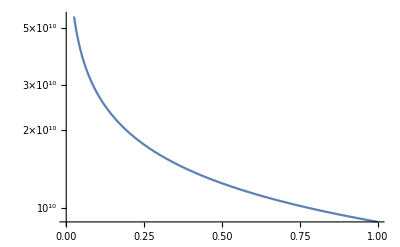

```mathematica
LogPlot[quadCutOff[10^16,r],{r,0,1}]
```

Here, I change the mass formula to make a huge number of very close sectors - this isn’t realistic, but more of a proof of principle

```mathematica
mHi[N_,r_,i_]= 60 + 10*(-i-1)(*i negative in this case - independent of N, just in so it has the same form as from the paper*)
```

60+10 (-1-i)

```mathematica
mH1 =mHi[10^8,1,-1]
```

60

## Degrees of Freedom

#### Exotic Sector Evolution

Note: The exotic sector has 118 degrees of freedom at high energies: 72 from quarks,  12 from charged leptons, 6 from neutrinos, 16 from gluons, 2 from photons, 6 from W bosons (no symmetry breaking = no longitudinal modes), 4 from the higgs sector (no symmetry breaking = 3 extra modes), for a total of 118 dof (28 bosonic and 90 fermionic) = 106.75 effective relativistic dof.  After the higgs freeze out, 4 edof are lost; when the QCD phase transition occurs

```mathematica
geHE =106.75
geBH = 102.75
geBQCD = 56.75
```

106.75

102.75

56.75

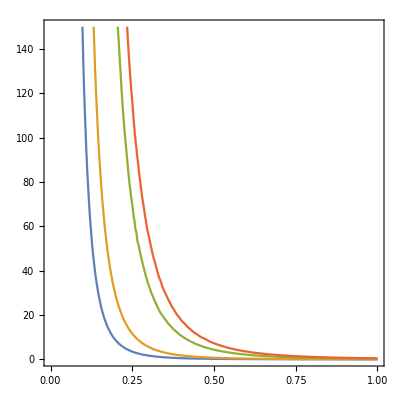

```mathematica
ContourPlot[{(4/7)*(11/4)^(4/3) gh * ξ^4==0.03,(4/7)*(11/4)^(4/3) gh * ξ^4==0.1,(4/7)*(11/4)^(4/3) gh * ξ^4==0.6,(4/7)*(11/4)^(4/3) gh * ξ^4==1},{ξ, 0, 1},{gh,0,150}]
```

```mathematica
ΔNeffweird = Sum[(4/7)(11/4)^(4/3)*gh*(1.467*0.062*(mHi[10^8,1,-1]/mHi[10^8,1,-i]))^4,{i,100}] (*starting value taken for 100 GeV reheaton, the 1.517 adjustst the temp of the original calculation to this new format*)
```

0.000384877 gh

Worst case scenario is where all exotic sector pions are still thermal and relativistic, leptons are still thermal and relativistic, and photons and massless Ws are thermal.

```mathematica
ghwc = 35 + (7/8)*18 + 6
```

227/4

```mathematica
N[ghwc]
```

56.75

```mathematica
worstCase = ΔNeffweird /. gh -> ghwc
```

0.0218418